### Naloga 1

```mathematica
d = Daljica[{-1,1},{3,-1}]
d2 = Daljica[{-1, -1}, {3, 1}]
d3 = Daljica[{-1, 2}, {3, 0}]
```

Daljica[{-1,1},{3,-1}]

Daljica[{-1,-1},{3,1}]

Daljica[{-1,2},{3,0}]

```mathematica
Dolzina[Daljica[AA_, BB_]] := Norm[BB -AA]
```

```mathematica
Dolzina[d]
```

2 √5

```mathematica
Slika[Daljica[AA_,BB_]] := Line[{AA, BB}]
```

```mathematica
Slika[d]
```

Line[{{-1,1},{3,-1}}]

```mathematica
Narisi[d_Daljica] := Graphics[Slika[d]]
Narisi[d__Daljica] := Graphics[Map[Slika, List[d]]]
```

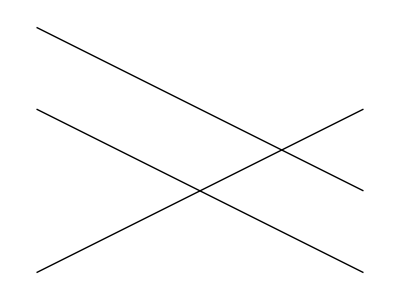

```mathematica
Narisi[d, d2, d3]
```

```mathematica
ClearAll[x, y]
EnacbaNosilke[Daljica[AA_,BB_]] := Module[{x1, y1, x2, y2, k, n},
{x1, y1}=AA;
{x2, y2}=BB;
k = (y2 - y1)/(x2 - x1);
n =n /.First[Solve[y1 == k*x1 + n, n]];
y ==  k*x + n
]
```

```mathematica
EnacbaNosilke[d]
```

y==1/2-x/2

### Naloga 2

```mathematica
Presek[Daljica[AA_,BB_],Daljica[CC_,DD_]]:= Module[{resitev},
resitev = Solve[{AA + r(BB - AA) == CC + s(DD - CC), r ≥ 0, r ≤ 1, s ≥ 0, s ≤ 1}, {r, s}];
If[resitev == {},
{},
First[AA + r(BB - AA) /. resitev]
]
]
```

```mathematica
Presek[d, d2]
```

{1,0}

```mathematica
Presek[d, d3]
```

{}

### Naloga 3

```mathematica
m1 = {{0,0},{11,1},{3,1},{-1,2}}
```

{{0,0},{11,1},{3,1},{-1,2}}

```mathematica
m2={{2,3},{1,9},{4,2},{7,0},{1,3}}
```

{{2,3},{1,9},{4,2},{7,0},{1,3}}

```mathematica
Slika[Mnogokotnika[t__]]:=Map[Line,List[t]]
```

```mathematica
Slika[Mnogokotnika[m1]]
```

{Line[{{0,0},{11,1},{3,1},{-1,2}}]}

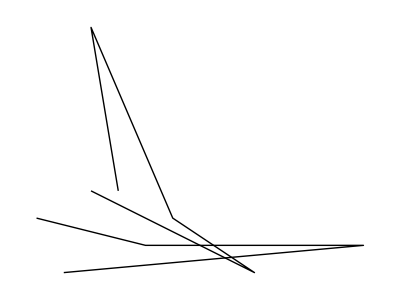

```mathematica
Graphics[Slika[Mnogokotnika[m1,m2]]]
```

```mathematica
Narisi[m__Mnogokotnika]:=Graphics[Map[Slika,List[m]]]
```

```mathematica
Narisi[m1]
```

Narisi[{{0,0},{11,1},{3,1},{-1,2}}]

```mathematica
NarobePravilniNKotnik[n_,r_]:=Module[{tocke, stej},
tocke =Table[{r Cos[(2 Pi + stej) /n], r Sin[(2 Pi + stej)/ n]},{stej,0,n - 1,1}];
Graphics[Slika[Mnogokotnika[tocke],Point[{0,0}]]]
]
```

```mathematica
Table[{5 Cos[(2 Pi + stej) /5], 5 Sin[(2 Pi + stej)/ 5]},{stej,0,4,1}]
```

{{5/4 (-1+√5),5 √(5/8+(√5)/8)},{5 Cos[1/5 (1+2 π)],5 Sin[1/5 (1+2 π)]},{5 Cos[1/5 (2+2 π)],5 Sin[1/5 (2+2 π)]},{5 Cos[1/5 (3+2 π)],5 Sin[1/5 (3+2 π)]},{5 Cos[1/5 (4+2 π)],5 Sin[1/5 (4+2 π)]}}

```mathematica
PravilniNKotnik[n_,r_]:= Graphics[{Line[Table[{r* Cos[(2Pi * i)/n],r*Sin[(2 Pi *i)/n]},{i,0,n}]]},{Point[{0,0}]}]
```

```mathematica
PravilniNKotnik[5,2]
```

-Graphics-

### Naloga 4

```mathematica
Prazeb[m_Mnogokotnikk, d_Daljica]:=Module[{resitev,dal},
del=EnacbaNosilke[d];
resitev = Solve[{AA + r(BB - AA) == CC + s(DD - CC), r ≥ 0, r ≤ 1, s ≥ 0, s ≤ 1}, {r, s}];
]
```

### Naloga 5

```mathematica
VsiPari[f_,sez1_,sez2_]:=Flatten[Outer[f, sez1,sez2],1]
```

```mathematica
VsiPari[f,{1,2,3},{a,b}]
```

{f[1,a],f[1,b],f[2,a],f[2,b],f[3,a],f[3,b]}

```mathematica
f[x_,y_]:=x / y
```

```mathematica
VsiPari[f,{1,2,3},{-9,6,10,2}]
```

{-1/9,1/6,1/10,1/2,-2/9,1/3,1/5,1,-1/3,1/2,3/10,3/2}

```mathematica
g[m1_Mnogokotnika,m2_Mnogotnika]:=Presek[m1,m2]
```

```mathematica
Presek[m1_Mnogokotnika,m2_Mnogkotnika]:=VsiPari[g,m1,m2]
```

### Naloga 6

```mathematica
Normala[p_,{u_,v_}]:=Module[{levidel},
levidel=(p[[1]]-p[[2]])/.{x->-y,y->x};
Return[levidel==(levidel/.{x->u,y->v})]]
```

```mathematica
Normala[2 x - 3 y == 2, {1,9}]
```

-2-3 x-2 y==-23

#### Izračuna normalo na premico v dani točki. V R^2 prostoru. /. pomoni da namesto x iny vstavi kar je na drugi strani -> .